```mathematica
Import["/home/jadeleon/Documents/pce/mathematica/pce.m"]
```

## Hermanitos PCE

```mathematica
generatorsTwoQubits=ArrayReshape[Diagonal/@PCEgenerators[2],{15,4,4}];
```

```mathematica
OneFourthInvariantTwoQubits=Erase[generatorsTwoQubits,generatorsTwoQubits,4];
OneEigthInvariantTwoQubits=Erase[generatorsTwoQubits,OneHalfInvariantTwoQubits,2];
```

```mathematica
TwoQBoard/@generatorsTwoQubits
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
hermanitosOneHalfAndOneEigth={TwoQBoard@generatorsTwoQubits[[#[[1]]]],TwoQBoard@OneFourthInvariantTwoQubits[[#[[2]]]]}&/@{{1,4},{2,8},{3,12},{4,1},{8,1},{12,2},{5,5},{6,9},{7,13},{9,6},{10,10},{11,14},{13,7},{14,11},{15,15}};
```

```mathematica
hermanitosOneHalfAndOneEigth//Transpose//GraphicsGrid
```

-Graphics-

Nótese que los primeros 6 se pueden escribir de la forma ℰ⊗𝕀 o 𝕀⊗ℰ, con ℰ un canal cuántico PCE de 1 qubit.

```mathematica
KroneckerProduct[{1,1,0,0},{1,1,0,0}]+KroneckerProduct[{0,0,1,1},{0,0,1,1}]//TwoQBoard
```

-Graphics-

El resto son de la forma ℰ⊗ℰ+Λ, con Λ una operación que deja invariante el resto de las componentes.

```mathematica
KroneckerProduct[{1,0,1,0},{1,1,0,0}]//TwoQBoard
```

-Graphics-

```mathematica
OneQubitPCE={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}};
```

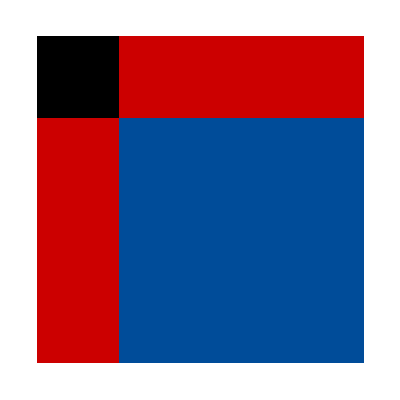
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TwoQBoard/@Flatten[Table[KroneckerProduct[OneQubitPCE[[i]],OneQubitPCE[[j]]]+KroneckerProduct[{1,1,1,1}-OneQubitPCE[[i]],{1,1,1,1}-OneQubitPCE[[j]]],{i,4},{j,4}],1]
```

```mathematica
DeleteDuplicates@ArrayReshape[Table[KroneckerProduct[KroneckerProduct[OneQubitPCE[[i]],OneQubitPCE[[j]]],OneQubitPCE[[k]]]+KroneckerProduct[KroneckerProduct[{1,1,1,1}-OneQubitPCE[[i]],{1,1,1,1}-OneQubitPCE[[j]]],{1,1,1,1}-OneQubitPCE[[k]]],{i,4},{j,4},{k,4}],{64,4,4,4}]//Length
```

64

```mathematica
Cube3q[Flatten@KroneckerProduct[{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{1,1,0,0}]+Flatten@KroneckerProduct[ConstantArray[1,{4,4}]-{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{1,1,1,1}-{1,1,0,0}]]
```

-Graphics3D-

```mathematica
Cube3q@ArrayReshape[KroneckerProduct[KroneckerProduct[OneQubitPCE[[1]],OneQubitPCE[[2]]],OneQubitPCE[[3]]]+KroneckerProduct[KroneckerProduct[{1,1,1,1}-OneQubitPCE[[1]],{1,1,1,1}-OneQubitPCE[[2]]],{1,1,1,1}-OneQubitPCE[[3]]],{4,4,4}]
```

-Graphics3D-

```mathematica
Cube3q@Normal[SparseArray[{{1,1,1},{2,3,4}}->{1,1},{4,4,4}]]-1
```

-1+-Graphics3D-